# Large-Amplitude Elongated-Body Theory of Fish Locomotion

```mathematica
x[a_,t_]:=c*t*a;
(*z[a_,t_]:=d*t^2*a^3;*)
ρ=1;
s=1;
l=1;
k=(2*π)/(.95*l)
ω=(2*π*0.3)/(2*0.1)
t={0,0.1, 0.2, 0.3, 0.5,1,2,4,9,10,20}
```

SetDelayed::write: Tag List in {0,0.5 a c,a c,2 a c,4 a c,9 a c,10 a c,20 a c}[a_,t_] is Protected.

6.61388

9.42478

{0,0.1,0.2,0.3,0.5,1,2,4,9,10,20}

```mathematica
{0,0.1, 0.2, 0.3, 0.5,1,2,4,9,10,20}
```

{0,0.1,0.2,0.3,0.5,1,2,4,9,10,20}

```mathematica
a c t
```

a c t

```mathematica
Clear[z]
```

```mathematica
h[z_]=(0.002-0.08*z+0.16*z^2)*Sin[k*z-ω*t]
```

{(0.002-0.08 z+0.16 z^2) Sin[0.+6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[0.942478-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[1.88496-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[2.82743-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[4.71239-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[9.42478-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[18.8496-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[37.6991-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[84.823-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[94.2478-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[188.496-6.61388 z]}

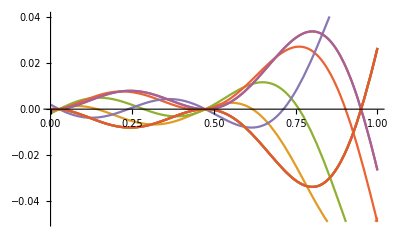

```mathematica
Plot[h,{z,0,1}]
```

```mathematica
u=D[x,t]*D[x,a]+D[z,t]*D[z,a]
w = D[z,t]*D[x,a]-D[x,t]*D[z,a]
```

a c^2 t+6 a^5 d^2 t^3

-a^3 c d t^2

Added mass per unit length

```mathematica
m=1/4 π*ρ*s^2
```

π/4

```mathematica
{P1,Q1}=(m*w*{D[z,t],-D[x,t]}-1/2 m*w^2*{D[x,a],D[z,a]})
{P2, Q2}=D[Integrate[m*w*{-D[z,a],D[x,a]},{a,0,l}],t]
```

{-1/2 a^6 c d^2 π t^3-1/8 a^6 c^3 d^2 π t^5,1/4 a^4 c^2 d π t^2-3/8 a^8 c^2 d^3 π t^6}

{2048 c d^2 π t^3,-48 c^2 d π t^2}

```mathematica
{P,Q}=({P1,Q1}/.a-> 0)-{P2, Q2}
```

{-2048 c d^2 π t^3,48 c^2 d π t^2}